# Introduction to Mathematical Epidemiology

Notes to accompany course material for PH252B

## Ch 2: Introduction to Epidemic Modeling

### 2.1 Kermack-McKendrick SIR Epidemic Model

```mathematica
SIRclosed={
S'[t]==-β i[t] S[t],
i'[t]==β i[t] S[t]-α i[t],
R'[t]==α i[t],
S[0]==100-1,i[0]==1,R[0]==0
};
{β,α,tmax}={.01,1/2,100};
SIRcloseSoln=NDSolve[SIRclosed,{S,i,R},{t,0,tmax}];
```

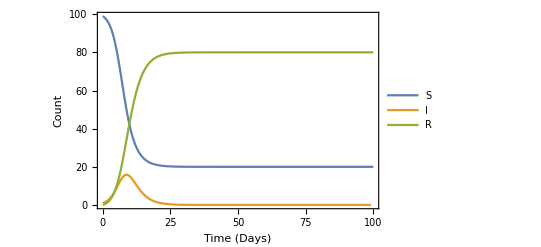

```mathematica
Plot[
{
S[t]/.SIRcloseSoln,
i[t]/.SIRcloseSoln,
R[t]/.SIRcloseSoln
},
{t,0,tmax},Frame->True,PlotLegends->Flatten[{"S","I","R"}],FrameLabel->{"Time (Days)","Count"},PlotRange->{0,All}
]
```

One can also calculate the final size of the epidemic

```mathematica
99*ⅇ^(-β/α 100)
```

13.3982

As well as maximum severity of epidemic

```mathematica
-α/β+α/β Log[α/β]+99+1-α/β Log[99]
```

15.8452

### 2.2 Estimating Parameters from Data

We note that the number of individuals in the I class at any time t is given by an exponential function; thus for a given cohort of infecteds, the fraction of individuals who have left the infected compartment is given by the exponential distribution parameterized by alpha; mean time spent in the infectious class is the inverse of alpha.

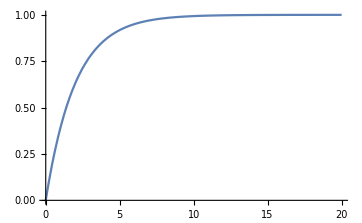

```mathematica
Plot[1-ⅇ^(-α x),{x,0,20},PlotRange->All]
```

### 2.3 A Simple SIS Epidemic Model

```mathematica
SISclosed={
s'[t]==-β i[t] s[t] +α i[t],
i'[t]==β i[t] s[t]-α i[t],
s[0]==1000-1,i[0]== 1
};
{β,α,tmax}={.001,1/5,100};
SIScloseSoln=NDSolve[SISclosed,{s,i},{t,0,tmax}];
```

The basic reproductive number can be calculated from the SIS model as below. This equation is because the classic R0 applies in a population of only susceptibles, that is why we multiply beta, the effective contact rate, by N as we assume all N people are S. We divide by alpha because beta*N is number of secondary cases produced per unit of time, and the infection lasts for 1/alpha time.

```mathematica
(β 1000)/α
```

5.

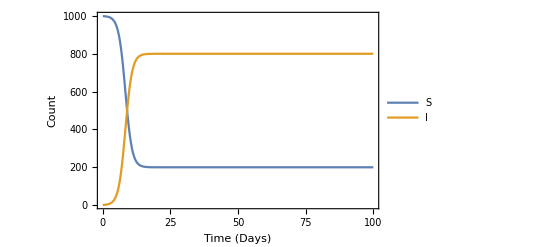

```mathematica
Plot[
{
s[t]/.SIScloseSoln,
i[t]/.SIScloseSoln
},
{t,0,tmax},Frame->True,PlotLegends->Flatten[{"S","I"}],FrameLabel->{"Time (Days)","Count"},PlotRange->{0,All}
]
```

It is possible to reduce the SIS model to a logistic equation because N is fixed.

```mathematica
{r,K}={β 1000-α,r/β};
SISlogistic={
i'[t]==r i[t](1-i[t]/K),
i[0]==1
};
SISlogisticSoln=NDSolve[SISlogistic,{i},{t,0,tmax}];
```

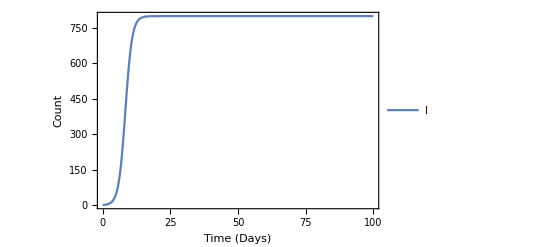

```mathematica
Plot[
{
i[t]/.SISlogisticSoln
},
{t,0,tmax},Frame->True,PlotLegends->{"I"},FrameLabel->{"Time (Days)","Count"},PlotRange->{0,All}
]
```

Solutions to the logistic equation always converge to the endemic equilibrium

```mathematica
logisticEquilibrium=Flatten[Function[i0,NDSolve[{
i'[t]==r i[t](1-i[t]/K),
i[0]==i0
},{i},{t,0,tmax}]]/@{1,50,800,1000,1500}];
```

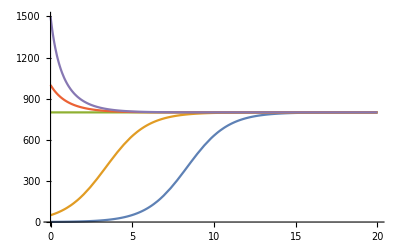

```mathematica
#[t]&/@logisticEquilibrium[[All,2]]//
Plot[#,{t,0,20},PlotRange->All]&
```

Graphical analysis of equilibria and stability; negative slopes correspond to local stability, positive slopes correspond to instability, and stability cannot be determined for slope of 0.

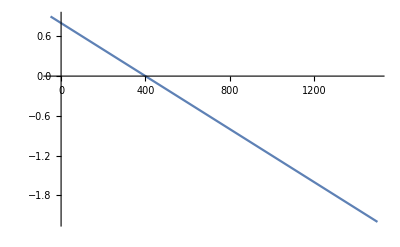

```mathematica
Plot[
{r (1-i/K)-r/K i},{i,-50,1500},PlotRange->All
]
```

### 2.4 An SIS Epidemic Model with Saturating Treatment

## Ch 3: The SIR Model with Demography: General Properties of Planar Systems